```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_1"];
LNDatabeta006=ReadList["LNData_NM_beta_0.06.txt"];
LNDatabeta012=ReadList["LNData_NM_beta_0.12.txt"];
LNDatabeta018=ReadList["LNData_NM_beta_0.18.txt"];
LNDatabeta024=ReadList["LNData_NM_beta_0.24.txt"];
LNDatabeta030=ReadList["LNData_NM_beta_0.3.txt"];
LNDatabeta031=ReadList["LNData_NM_beta_0.31.txt"];
LNDatabeta032=ReadList["LNData_NM_beta_0.32.txt"];
LNDatabeta033=ReadList["LNData_NM_beta_0.33.txt"];
LNDatabeta034=ReadList["LNData_NM_beta_0.34.txt"];
LNDatabeta035=ReadList["LNData_NM_beta_0.35.txt"];
LNDatabeta036=ReadList["LNData_NM_beta_0.36.txt"];
LNDatabeta037=ReadList["LNData_NM_beta_0.37.txt"];
LNDatabeta038=ReadList["LNData_NM_beta_0.38.txt"];
LNDatabeta039=ReadList["LNData_NM_beta_0.39.txt"];
LNDatabeta040=ReadList["LNData_NM_beta_0.4.txt"];
LNDatabeta041=ReadList["LNData_NM_beta_0.41.txt"];
LNDatabeta042=ReadList["LNData_NM_beta_0.42.txt"];
LNDatabeta048=ReadList["LNData_NM_beta_0.48.txt"];
LNDatabeta054=ReadList["LNData_NM_beta_0.54.txt"];
LNDatabeta060=ReadList["LNData_NM_beta_0.6.txt"];
LNDatabeta066=ReadList["LNData_NM_beta_0.66.txt"];
LNDatabeta072=ReadList["LNData_NM_beta_0.72.txt"];
LNDatabeta078=ReadList["LNData_NM_beta_0.78.txt"];
LNDatabeta084=ReadList["LNData_NM_beta_0.84.txt"];
LNDatabeta090=ReadList["LNData_NM_beta_0.9.txt"];
LNDatabeta096=ReadList["LNData_NM_beta_0.96.txt"];
```

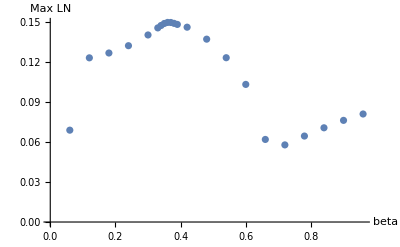

```mathematica
ListPlot[{
{0.06, Max[Table[LNDatabeta006[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.12, Max[Table[LNDatabeta012[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.18, Max[Table[LNDatabeta018[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.24, Max[Table[LNDatabeta024[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.30, Max[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.33, Max[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.34, Max[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.35, Max[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.36, Max[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.37, Max[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.38, Max[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.39, Max[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.42, Max[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.48, Max[Table[LNDatabeta048[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.54, Max[Table[LNDatabeta054[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.60, Max[Table[LNDatabeta060[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.66, Max[Table[LNDatabeta066[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.72, Max[Table[LNDatabeta072[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.78, Max[Table[LNDatabeta078[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.84, Max[Table[LNDatabeta084[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.90, Max[Table[LNDatabeta090[[1]][[pt]][[2]], {pt, 1, 1000}]]},
{0.96, Max[Table[LNDatabeta096[[1]][[pt]][[2]], {pt, 1, 1000}]]}
}, AxesLabel->{"beta", "Max LN"}, Joined->False]
```

```mathematica
(* Construct 3D graph with axes, time, β, and LN, inserting the beta value (Δβ = 0.06) for the file as 2nd element *)
beta006=Table[Table[{LNDatabeta006[[pair]][[pt]][[1]], 0.06, LNDatabeta006[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta012=Table[Table[{LNDatabeta012[[pair]][[pt]][[1]], 0.12, LNDatabeta012[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta018=Table[Table[{LNDatabeta018[[pair]][[pt]][[1]], 0.18, LNDatabeta018[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta024=Table[Table[{LNDatabeta024[[pair]][[pt]][[1]], 0.24, LNDatabeta024[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta030=Table[Table[{LNDatabeta030[[pair]][[pt]][[1]], 0.30, LNDatabeta030[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta036=Table[Table[{LNDatabeta036[[pair]][[pt]][[1]], 0.36, LNDatabeta036[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta042=Table[Table[{LNDatabeta042[[pair]][[pt]][[1]], 0.42, LNDatabeta042[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta048=Table[Table[{LNDatabeta048[[pair]][[pt]][[1]], 0.48, LNDatabeta048[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta054=Table[Table[{LNDatabeta054[[pair]][[pt]][[1]], 0.54, LNDatabeta054[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta060=Table[Table[{LNDatabeta060[[pair]][[pt]][[1]], 0.60, LNDatabeta060[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta066=Table[Table[{LNDatabeta066[[pair]][[pt]][[1]], 0.66, LNDatabeta066[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta072=Table[Table[{LNDatabeta072[[pair]][[pt]][[1]], 0.72, LNDatabeta072[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta078=Table[Table[{LNDatabeta078[[pair]][[pt]][[1]], 0.78, LNDatabeta078[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta084=Table[Table[{LNDatabeta084[[pair]][[pt]][[1]], 0.84, LNDatabeta084[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta090=Table[Table[{LNDatabeta090[[pair]][[pt]][[1]], 0.90, LNDatabeta090[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
beta096=Table[Table[{LNDatabeta096[[pair]][[pt]][[1]], 0.96, LNDatabeta096[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
```

```mathematica
(* Extracting the data of each LN pair in the order: LN12, LN13=LN24, LN14=LN23, LN34 *)
betaData={
{beta006[[1]], beta006[[2]], beta006[[4]], beta006[[6]]},
{beta012[[1]], beta012[[2]], beta012[[4]], beta012[[6]]},
{beta018[[1]], beta018[[2]], beta018[[4]], beta018[[6]]},
{beta024[[1]], beta024[[2]], beta024[[4]], beta024[[6]]},
{beta030[[1]], beta030[[2]], beta030[[4]], beta030[[6]]},
{beta036[[1]], beta036[[2]], beta036[[4]], beta036[[6]]},
{beta042[[1]], beta042[[2]], beta042[[4]], beta042[[6]]},
{beta048[[1]], beta048[[2]], beta048[[4]], beta048[[6]]},
{beta054[[1]], beta054[[2]], beta054[[4]], beta054[[6]]},
{beta060[[1]], beta060[[2]], beta060[[4]], beta060[[6]]},
{beta066[[1]], beta066[[2]], beta066[[4]], beta066[[6]]},
{beta072[[1]], beta072[[2]], beta072[[4]], beta072[[6]]},
{beta078[[1]], beta078[[2]], beta078[[4]], beta078[[6]]},
{beta084[[1]], beta084[[2]], beta084[[4]], beta084[[6]]},
{beta090[[1]], beta090[[2]], beta090[[4]], beta090[[6]]},
{beta096[[1]], beta096[[2]], beta096[[4]], beta096[[6]]}};
```

```mathematica
(* Getting plot format correct for the 3D plot for one example *)
PlotFormat={PlotRange->{{0, 500}, {0.006, 0.96}, {0, 3}}, Filling->None, PlotStyle->Directive[PointSize->0.002], AxesLabel->{"τ", "β", "ℒ𝒩"}, LabelStyle->Directive[Black, FontSize->11, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[beta, {beta, 0.06, 0.96, 0.06}], Automatic}};
ListPointPlot3D[betaData[[4]], Evaluate[PlotFormat]]
```

-Graphics3D-

```mathematica
betaplots=Table[ListPointPlot3D[betaData[[n]], Evaluate[PlotFormat]], {n, 1, Length[betaData]}];
NonMarkovianSystemBeta=Show[betaplots, BoxRatios->{3.5, 3.5, 3.5}, ImageSize->Large, ViewPoint->{2.5, -2.5, 1.7}]
```

-Graphics3D-

Finding:
	We notice that the LN for pair 1,3 and pair 2,4 equals zero or effectively zero and this is true for pair 1,4 and pair 2,3. When η is positive we found that pair 1,3 = 2,4 and pair 1,4=2,3 already has a small amount of entanglement increase in comparison to pair 1,2. If this ratio is maintained then the entanglement transfer to pair 1,3 = 2,4 and pair 1,4=2,3 via indirect entanglement transfer would also be small in comparison to 1,2. We found pair 1,2 to have a small amount of entanglement increase, satisfying this ratio would put those other pairs to have effectively zero entanglement. Since the nearest neighbor coupling, η = 0, this means that entanglement must have transferred through the non-Markovian environment. This entanglement transfer is indirect because it requires the entanglement to leak from pair 3,4 into the non-Markovian environment and then come back, via the memory effect, to the system and cause pair 1,2 to become entangled.
	If we look at the Closed environment, β = 0, or Markovian Environment, β = 0.06, both do not show any LN increase for pair 1,2 and it remains zero for all time simulated. For the Closed environment, we have pair 3,4 remain constant whereas the Markovian environment, we have pair 3,4 decaying. This makes intuitive sense because in a Closed environment, there’s nowhere for the entanglement to go given that η = 0, so it just remains within pair 3,4 because it was initialized as a two-mode squeezed state to begin with. For the Markovian environment, we have the decay because the environment just sucks away the information and information never returns back to the system so no pair combination gains any entanglement.

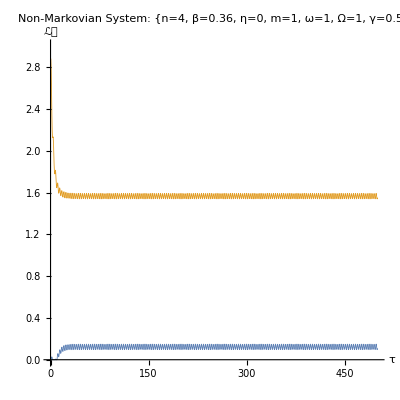

```mathematica
(* Plot Formatting *)
height=400;
width=400;
PlotFormat={Joined->True, PlotRange->{0, 3}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "ℒ𝒩"}, AxesStyle->Directive[Black,15], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 15], PlotStyle->{Thickness[0.0015]}};

(* Plot LN12 and LN34 for a specific value of β *)
LNPlot=ListPlot[{LNDatabeta036[[1]], LNDatabeta036[[6]]}, PlotLabel->"Non-Markovian System: {n=4, β=0.36, η=0, m=1, ω=1, Ω=1, γ=0.5}",  Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->None]
```

```mathematica
(* Organizing data for LN12 and LN24 as a function of β *)
betaLNPlots={
ListPlot[{LNDatabeta006[[1]], LNDatabeta006[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.06, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta012[[1]], LNDatabeta012[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.12, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta018[[1]], LNDatabeta018[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.18, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta024[[1]], LNDatabeta024[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.24, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta030[[1]], LNDatabeta030[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.30, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta036[[1]], LNDatabeta036[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.36, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta042[[1]], LNDatabeta042[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.42, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta048[[1]], LNDatabeta048[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.48, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta054[[1]], LNDatabeta054[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.54, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta060[[1]], LNDatabeta060[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.60, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta066[[1]], LNDatabeta066[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.66, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta072[[1]], LNDatabeta072[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.72, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta078[[1]], LNDatabeta078[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.78, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta084[[1]], LNDatabeta084[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.84, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta090[[1]], LNDatabeta090[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.90, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]],
ListPlot[{LNDatabeta096[[1]], LNDatabeta096[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.96, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]]
};
```

```mathematica
(* Animate LN12 and LN34 as β varies *)
ListAnimate[betaLNPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

Finding:
	We find that the saturated value of LN12 increases for β = 0.06 to 0.36 and then decreases afterwards. Also, LN for both pair 1,2 and pair 3,4 approaches towards this saturated value faster as β increases and once the graphs are effectively constant, they remain constant but decrease for every increase in β. (We know that ω = Ω is the reason that the graphs approach a constant.) There exists a maximum β value that maximizes LN12. This maximum seems to occur when β = 0.36.

```mathematica
Length[LNDatabeta033[[1]]]
```

1001

```mathematica
(* Finding β to maximize LN12: We find the maximum value for the LN12 data as a function of time for each β value. *)
MaxBetaData={
{0.33, Max[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.34, Max[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.35, Max[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.36, Max[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.37, Max[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.38, Max[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.39, Max[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 1, 1001}]]}};

(* Create an interpolated function based on the points *)
iMaxBetafunc=Interpolation[MaxBetaData];
```

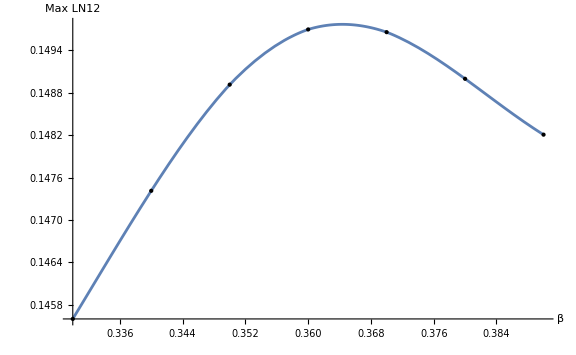

```mathematica
(* We plot the maximum values of LN12 as a function of β as points and have our interpolated function plotted with them. *)
Plot[iMaxBetafunc[x], {x, 0.33, 0.39}, Epilog->Point[MaxBetaData], AxesLabel->{"β", "Max LN12"}, LabelStyle->Directive[Black, FontSize->15, FontFamily->"Latin Modern Roman"], ImageSize->Large]
```

```mathematica
(* Find the max value of LN12 by taking the derivative of the interpolated function with respect to β and setting equal to zero, then solving... *)
βmax=Flatten[Solve[D[iMaxBetafunc[β], β]==0, β]][[1]][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.364358

Interpolated function's prediction for LN12 = 0.149767

Simulated data's value for LN12 = 0.149756

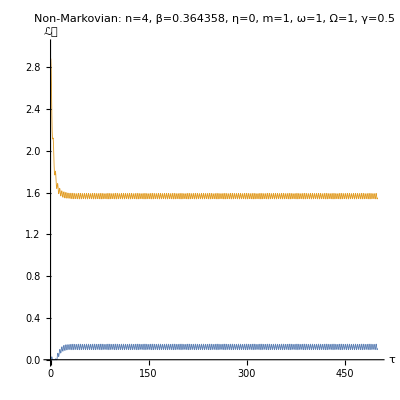

The percent difference of the Maximum LN12 between our interpolated function and numerical simulation for β = 0.364358, is 0.00768752%

The Maximumn LN12 is ≈ 0.1497 when β = 0.364358

```mathematica
(* We simulate the system using βmax = 0.364358 and compare the LN12 value in simulation to the LN12 value using the interpolation function *)
LNDatabeta0364358=ReadList["LNData_NM_beta_0.364358.txt"];

(* Interpolated function's prediciton for LN12 *)
"Interpolated function's prediction for LN12 = "<>ToString[iMaxBetafunc[0.364358]]

(* Simulated data's value for LN12 *)
"Simulated data's value for LN12 = "<>ToString[Max[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 1, 1000}]]]

(* Percent Difference between interpolated function and numerical simulation at β=0.364358 *)
percentdiff=Abs[iMaxBetafunc[0.364358]-Max[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 1, 1000}]]]/Mean[{iMaxBetafunc[0.364358],Max[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 1, 1000}]]}]*100;

ListPlot[{LNDatabeta0364358[[1]], LNDatabeta0364358[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.364358, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]]

"The percent difference of the Maximum LN12 between our interpolated function and numerical simulation for β = 0.364358, is "<>ToString[percentdiff]<>"%"
"The Maximumn LN12 is ≈ 0.1497 when β = 0.364358"
```

Finding:
	We found the maximum LN12 value ~ 0.1497 when β = 0.364358. Now we must show this finding with a nice graph.

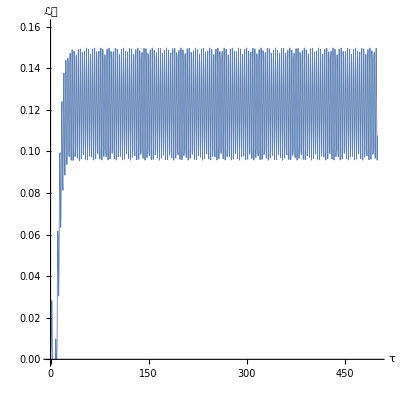

```mathematica
(* We will show the graph of LN12 as a function of time for β = 0.364358 *)
LN12maxbetaplot=ListPlot[LNDatabeta0364358[[1]], PlotRange->{0, 0.16}, Evaluate[PlotFormat]]
```

The graph of LN12 as a function of time for β = 0.364358 oscillates rapidly, so we will show a moving average overlaid on top and then report the min and max in the region of oscillation.

```mathematica
linecolors=Table[Blend[{Cyan, Magenta, Yellow}, i], {i, 0, 1, 0.25}]
```

{RGBColor[0., 1., 1.],RGBColor[0.5, 0.5, 1.],RGBColor[1., 0., 1.],RGBColor[1., 0.5, 0.5],RGBColor[1., 1., 0.]}

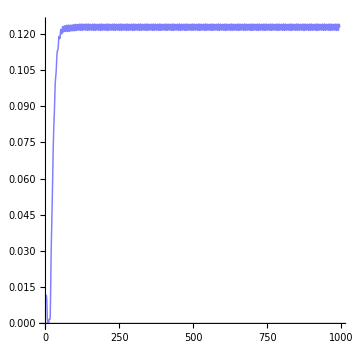

```mathematica
movavgvalue=6;
moavg0364358=MovingAverage[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue];
moavg0364358plot=ListPlot[moavg0364358, Joined->True, ImageSize->Medium, AspectRatio->1, PlotStyle->{Directive[Thickness->0.003, linecolors[[2]]]}]
```

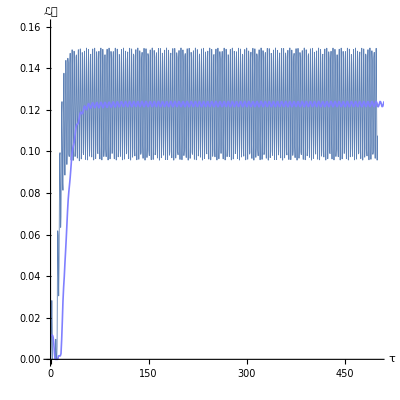

```mathematica
(* Show LN12 as a function of time and the moving average overlaid on top *)
Show[LN12maxbetaplot, moavg0364358plot]
```

```mathematica
(* We get min and max data points for β = 0.33 to 0.39 when LN12 is saturated which is approximately when t = 100 onwards *)
MinBetaData={
{0.30, Min[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.31, Min[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.32, Min[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.33, Min[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.34, Min[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Min[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.36, Min[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.37, Min[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.38, Min[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.39, Min[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Min[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.41, Min[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.42, Min[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 100, 1001}]]}};
MovavgBetaData={
{0.30, Mean[MovingAverage[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.31, Mean[MovingAverage[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.32, Mean[MovingAverage[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.33, Mean[MovingAverage[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.34, Mean[MovingAverage[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.35, Mean[MovingAverage[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.36, Mean[MovingAverage[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.37, Mean[MovingAverage[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.38, Mean[MovingAverage[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.39, Mean[MovingAverage[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.40, Mean[MovingAverage[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.41, Mean[MovingAverage[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]},
{0.42, Mean[MovingAverage[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]}};
MaxBetaData={
{0.30, Max[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.31, Max[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.32, Max[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.33, Max[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.34, Max[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.35, Max[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.36, Max[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.37, Max[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.38, Max[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.39, Max[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.40, Max[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.41, Max[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.42, Max[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 1, 1001}]]}};
```

```mathematica
minLN12=Min[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}]];
movavgLN12=Mean[MovingAverage[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]];
maxLN12=Max[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}]];
optimumLN12pt={0.364358, Around[movavgLN12, {movavgLN12-minLN12, maxLN12-movavgLN12}]}
```

{0.364358,0.1230.0270.027}

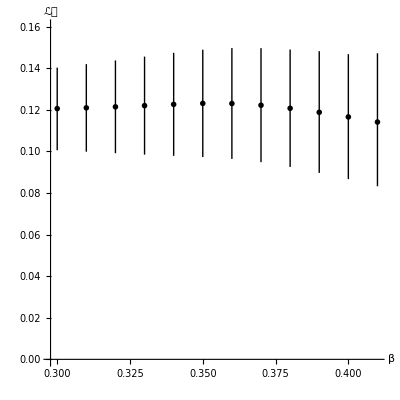

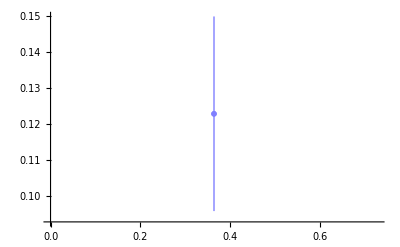

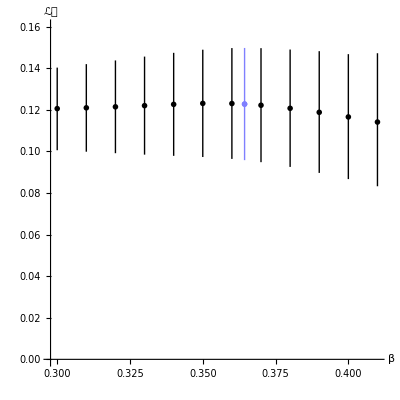

```mathematica
satLN12plot=ListPlot[Table[{MovavgBetaData[[pt]][[1]], Around[MovavgBetaData[[pt]][[2]], {MovavgBetaData[[pt]][[2]]-MinBetaData[[pt]][[2]], MaxBetaData[[pt]][[2]]-MovavgBetaData[[pt]][[2]]}]}, {pt, 1, 12}], PlotRange->{0, 0.16}, PlotMarkers->"OpenMarkers", PlotStyle->Directive[Black], ImageSize->{UpTo[width], UpTo[height]}, AxesLabel->{"β", "ℒ𝒩"}, AxesStyle->Directive[Black,15], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 15], PlotStyle->{Thickness[0.0015]}, AspectRatio->1]
satLN12plot2=ListPlot[{optimumLN12pt}, PlotRange->All, PlotMarkers->"OpenMarkers", PlotStyle->Directive[linecolors[[2]]]]
LN12optimumbetaplot=Show[satLN12plot, satLN12plot2]
```

```mathematica
Row[{Show[LN12maxbetaplot, moavg0364358plot], LN12optimumbetaplot}]
```

-Graphics--Graphics-

```mathematica
Max[MovingAverage[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]
Max[MovingAverage[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}],movavgvalue]]
```

0.124336

0.124096

Finding:
We find that the moving average graphs show a saturation value for LN that’s less than just the “max” value. The fluctuation goes up and down rapidly, so the value that matters more is the average value from 100 to 500. Just take the mean value of LN12 from t = 100 to 500, not moving average. Use moving average to show nice plots, but mention that there is a fluctuation. However, we find that the fluctuations are not the same for each value of β. Thus the saturated value of LN12 (the mean value from t = 100 to 500) for β = 0.364358 is less than for β = 0.36. In fact, we find that the maximum saturated value should be between β = 0.35 and 0.36.

0.124336

0.124096

```mathematica
MeanBetaData={
{0.30, Mean[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.31, Mean[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.32, Mean[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.33, Mean[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.34, Mean[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Mean[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.36, Mean[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.364358, Mean[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.37, Mean[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.38, Mean[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.39, Mean[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Mean[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.41, Mean[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.42, Mean[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

(* Create an interpolated function based on the points *)
iMeanBetafunc=Interpolation[MeanBetaData];
```

```mathematica
(* Plot Formatting *)
height=400;
width=400;
PlotFormat={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"β", "ℒ𝒩"}, AxesStyle->Directive[Black,15], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 15], PlotStyle->{Black, Thickness[0.003]}};
```

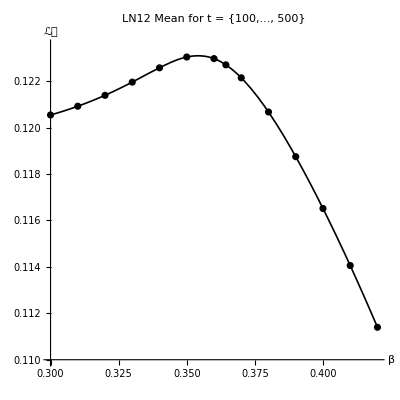

```mathematica
Show[{Plot[iMeanBetafunc[x], {x, 0.30, 0.42}, Evaluate[PlotFormat], PlotRange->{0.11, 0.1235}, PlotLabel->"LN12 Mean for t = {100,..., 500}"], ListPlot[MeanBetaData, Joined->False, Evaluate[PlotFormat]]}]
```

```mathematica
Mean[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]
Mean[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}]]
Mean[Table[LNDatabeta0364358[[1]][[pt]][[2]], {pt, 100, 1001}]]
```

0.123037

0.122969

0.1227

```mathematica
(* Find the max value of LN12 by taking the derivative of the interpolated function with respect to β and setting equal to zero, then solving... *)
sol=Flatten[Solve[D[iMeanBetafunc[β], β]==0, β]][[1]][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.354148

```mathematica
MeanBetaData//Column
```

{0.3,0.120541}
{0.31,0.120918}
{0.32,0.121388}
{0.33,0.121956}
{0.34,0.122572}
{0.35,0.123037}
{0.36,0.122969}
{0.364358,0.1227}
{0.37,0.122142}
{0.38,0.12067}
{0.39,0.118745}
{0.4,0.116514}
{0.41,0.114056}
{0.42,0.111397}

We see that the maximum value for the mean of LN12 for t = 100 to 500 is not when β = 0.364358, but rather when β = 0.354148. Let’s simulate the data for this β value and find the percent difference of our interpolated function and what the simulation produces.

Interpolated function's prediction for LN12 = 0.12309

Simulated data's value for LN12 = 0.123112

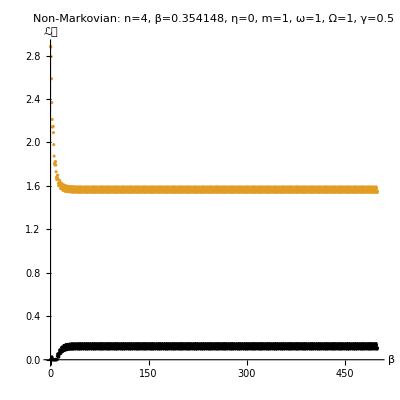

The percent difference of the mean value of LN12 for t = 100 to 500 between our interpolated function and numerical simulation for β = 0.354148, is 0.0178566%

```mathematica
(* We simulate the system using βmax = 0.354148 and compare the LN12 value in simulation to the LN12 value using the interpolation function *)
LNDatabeta0354148=ReadList["LNData_NM_beta_0.354148.txt"];

(* Interpolated function's prediciton for LN12 *)
"Interpolated function's prediction for LN12 = "<>ToString[iMeanBetafunc[0.354148]]

(* Simulated data's value for LN12 *)
"Simulated data's value for LN12 = "<>ToString[Mean[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1000}]]]

(* Percent Difference between interpolated function and numerical simulation at β=0.364358 *)
percentdiff=Abs[iMeanBetafunc[0.354148]-Mean[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1000}]]]/Mean[{iMeanBetafunc[0.354148],Mean[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1000}]]}]*100;

ListPlot[{LNDatabeta0354148[[1]], LNDatabeta0354148[[6]]}, PlotLabel->"Non-Markovian: n=4, β=0.354148, η=0, m=1, ω=1, Ω=1, γ=0.5", Evaluate[PlotFormat]]

"The percent difference of the mean value of LN12 for t = 100 to 500 between our interpolated function and numerical simulation for β = 0.354148, is "<>ToString[percentdiff]<>"%"
```

Let us now plot the mean values for LN12 for t = 100 to 500 and also plot the moving averages for visual clarity for β = 0.30 to 0.40

```mathematica
(* For Pair LN34 *)
MovavgBetaData1LN34={
MovingAverage[Table[LNDatabeta030[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta031[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta032[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta033[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta034[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta035[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta0354148[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta036[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta037[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta038[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta039[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta040[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta041[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta042[[6]][[pt]][[1]], {pt, 1, 1001}],movavgvalue]};

MovavgBetaData2LN34={
MovingAverage[Table[LNDatabeta030[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta031[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta032[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta033[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta034[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta035[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta0354148[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta036[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta037[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta038[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta039[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta040[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta041[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta042[[6]][[pt]][[2]], {pt, 1, 1001}],movavgvalue]};

MovavgBetaDataLN34=ArrayFlatten[Table[Table[{MovavgBetaData1LN34[[element]][[value]], MovavgBetaData2LN34[[element]][[value]]}, {value, 1, Length[MovavgBetaData1LN34[[element]]]}], {element, 1, 12}], 2];
```

```mathematica
(* For Pair LN12 *)

MinBetaData={
{0.30, Min[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.31, Min[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.32, Min[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.33, Min[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.34, Min[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Min[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.354148, Min[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.36, Min[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.37, Min[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.38, Min[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.39, Min[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Min[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.41, Min[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.42, Min[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

MeanBetaData={
{0.30, Mean[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.31, Mean[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.32, Mean[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.33, Mean[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.34, Mean[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Mean[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.354148, Mean[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.36, Mean[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.37, Mean[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.38, Mean[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.39, Mean[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Mean[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.41, Mean[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.42, Mean[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

MaxBetaData={
{0.30, Max[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.31, Max[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.32, Max[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.33, Max[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.34, Max[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.35, Max[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.354148, Max[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.36, Max[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.37, Max[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.38, Max[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.39, Max[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.40, Max[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.41, Max[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 1, 1001}]]},
{0.42, Max[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 1, 1001}]]}};

MovavgBetaData1={
MovingAverage[Table[LNDatabeta030[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta031[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta032[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta033[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta034[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta035[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta0354148[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta036[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta037[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta038[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta039[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta040[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta041[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta042[[1]][[pt]][[1]], {pt, 1, 1001}],movavgvalue]};

MovavgBetaData2={
MovingAverage[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta031[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta032[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta033[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta034[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta0354148[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta036[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta037[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta038[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta039[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta041[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue],
MovingAverage[Table[LNDatabeta042[[1]][[pt]][[2]], {pt, 1, 1001}],movavgvalue]};

MovavgBetaData=ArrayFlatten[Table[Table[{MovavgBetaData1[[element]][[value]], MovavgBetaData2[[element]][[value]]}, {value, 1, Length[MovavgBetaData1[[element]]]}], {element, 1, 12}], 2];
```

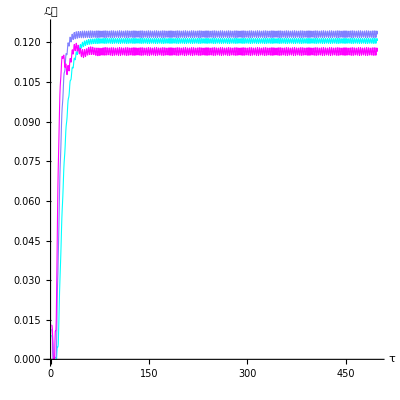
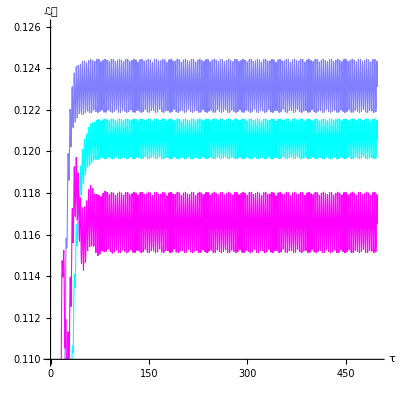

```mathematica
(* Plot Formatting for overall graph *)
height=400;
width=400;
PlotFormat1={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "ℒ𝒩"}, AxesStyle->Directive[Black,20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20], PlotStyle->{Black, Thickness[0.003]}};

(* Plot for LN12 *)
MovavgPlot1 = ListPlot[{MovavgBetaData[[1]], MovavgBetaData[[7]], MovavgBetaData[[12]]}, Joined->True, PlotRange->{0, 0.126}, PlotStyle->{Directive[linecolors[[1]], Thickness->0.002], Directive[linecolors[[2]], Thickness->0.002], Directive[linecolors[[3]], Thickness->0.002]}, Evaluate[PlotFormat1]];

(* Plot Formatting for zoomed graph *)
height=280;
width=280;
PlotFormat2={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width, AxesStyle->Directive[Black,16], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 16], PlotStyle->{Black, Thickness[0.003]}};
MovavgPlot2 = ListPlot[{MovavgBetaData[[1]], MovavgBetaData[[7]], MovavgBetaData[[12]]}, Joined->True, PlotRange->{0.11, 0.126}, PlotStyle->{Directive[linecolors[[1]], Thickness->0.002], Directive[linecolors[[2]], Thickness->0.002], Directive[linecolors[[3]], Thickness->0.002]}, AxesLabel->{"τ", "ℒ𝒩"},  Evaluate[PlotFormat2]];

(* Overlay the two graphs into one *)
MovavgPlot=Overlay[{MovavgPlot1, MovavgPlot2}, Alignment->{0.95, -0.15}]
```

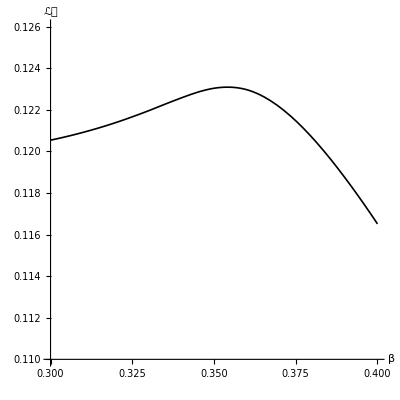

```mathematica
intlineplot=Plot[iMeanBetafunc[β], {β, 0.30, 0.40}, PlotRange->{0.11, 0.126},  AxesLabel->{"β", "ℒ𝒩"}, Evaluate[PlotFormat2]]
```

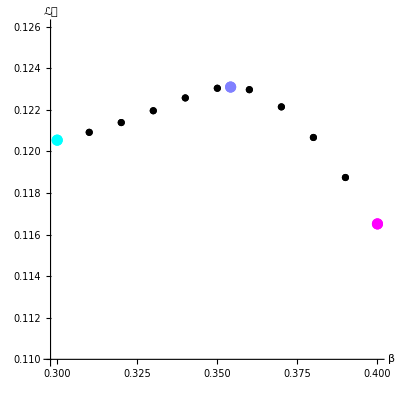

```mathematica
LN12MeanPlot=ListPlot[Table[{MeanBetaData[[pt]]}, {pt, 1, 12}], PlotRange->{0.11, 0.126}, AxesLabel->{"β", "ℒ𝒩"},  PlotStyle->{Directive[linecolors[[1]], PointSize[0.02]], Directive[Black], Directive[Black], Directive[Black], Directive[Black], Directive[Black] , Directive[linecolors[[2]], PointSize[0.02]], Directive[Black], Directive[Black], Directive[Black], Directive[Black], Directive[linecolors[[3]], PointSize[0.02]]}, Evaluate[PlotFormat2]]
```

```mathematica
BlankCanvas=ListPlot[{MovavgBetaData[[1]]}, Joined->True, PlotRange->{0, 0.126}, PlotStyle->{Directive[White]}, LabelStyle->Directive[White, 15], AxesStyle->Directive[White], Evaluate[PlotFormat1]];
zoomed=Overlay[{BlankCanvas, Show[{intlineplot, LN12MeanPlot}]}, Alignment->{-1, -0.15}];
```

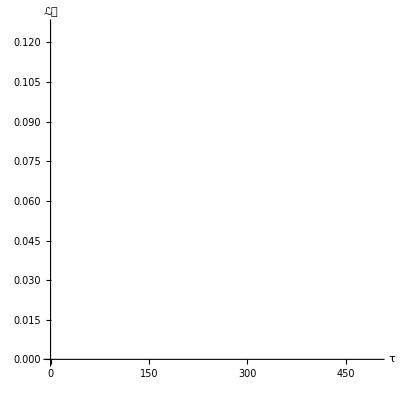
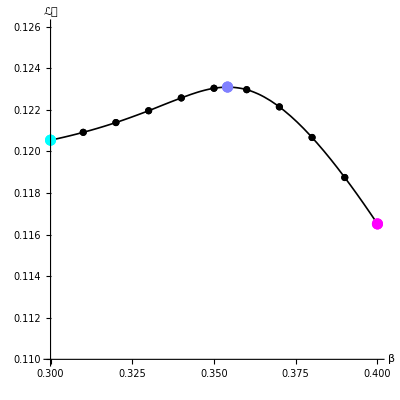
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Version1=Row[{MovavgPlot, zoomed}]
```

```mathematica
Export["betavary.png", Version1]
```

betavary.png

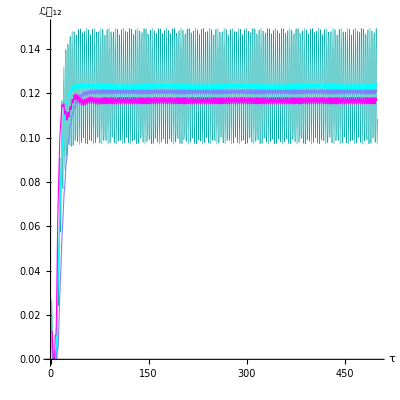
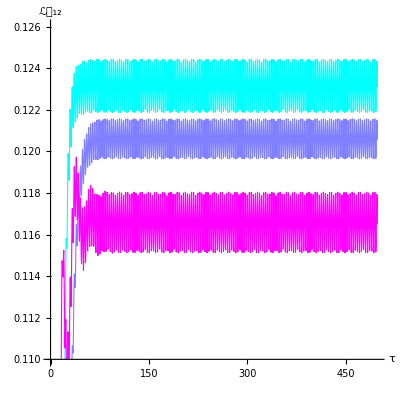
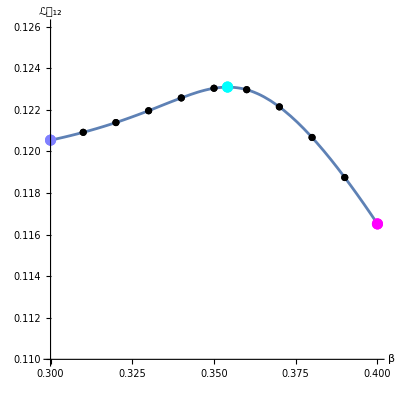

```mathematica
(* Plot Formatting for zoomed graph *)
height=400;
width=400;
PlotFormat3={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width, AxesStyle->Directive[Black,16], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 19]};

MovavgPlot2version2 = ListPlot[{MovavgBetaData[[1]], MovavgBetaData[[7]], MovavgBetaData[[12]]}, Joined->True, PlotRange->{0.11, 0.126}, PlotStyle->{Directive[linecolors[[2]], Thickness->0.002], Directive[linecolors[[1]], Thickness->0.002], Directive[linecolors[[3]], Thickness->0.002]}, AxesLabel->{"τ", "ℒ𝒩_12"},  Evaluate[PlotFormat3]];

LN12MeanPlotversion2=ListPlot[Table[{MeanBetaData[[pt]]}, {pt, 1, Length[MeanBetaData]}], PlotRange->{0.11, 0.126}, AxesLabel->{"β", "ℒ𝒩"},  PlotStyle->{Directive[linecolors[[2]], PointSize[0.02]], Directive[Black], Directive[Black], Directive[Black], Directive[Black], Directive[Black] , Directive[linecolors[[1]], PointSize[0.02]], Directive[Black], Directive[Black], Directive[Black], Directive[Black], Directive[linecolors[[3]], PointSize[0.02]]}, Evaluate[PlotFormat3]];

intlineplotversion2=Plot[iMeanBetafunc[β], {β, 0.30, 0.40}, PlotRange->{0.11, 0.126},  AxesLabel->{"β", "ℒ𝒩_12"}, Evaluate[PlotFormat3]];

LN12zoom=ListPlot[{LNDatabeta0354148[[1]], MovavgBetaData[[7]], MovavgBetaData[[1]], MovavgBetaData[[12]]}, Joined->True, PlotRange->{0, 0.15}, PlotStyle->{Directive[Darker[Cyan], Thickness->0.001], Directive[linecolors[[1]], Thickness->0.002], Directive[linecolors[[2]], Thickness->0.002], Directive[linecolors[[3]], Thickness->0.002] }, AxesLabel->{"τ", "ℒ𝒩_12"}, Evaluate[PlotFormat3]];

Version2=Row[{LN12zoom, MovavgPlot2version2, Show[intlineplotversion2, LN12MeanPlotversion2]}]
```

```mathematica
Export["betavary2.png", Version2]
```

betavary2.png

```mathematica
Export["betavary2a.png", LN12zoom]
Export["betavary2b.png", MovavgPlot2version2]
Export["betavary2c.png", Show[intlineplotversion2, LN12MeanPlotversion2]]
```

betavary2a.png

betavary2b.png

betavary2c.png

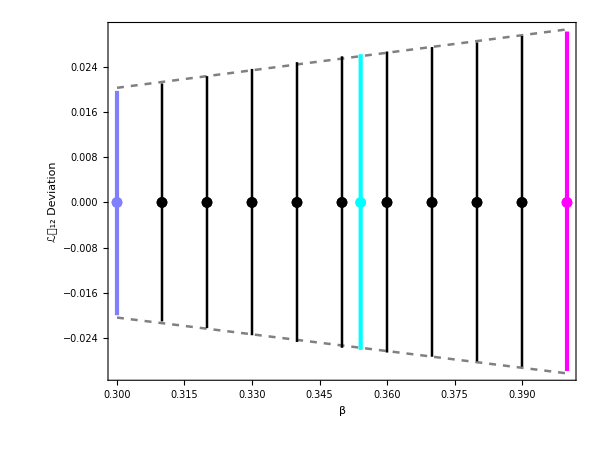

```mathematica
meanmin=Table[MeanBetaData[[pt]][[2]]-MinBetaData[[pt]][[2]], {pt, 1, 12}];
maxmean=Table[MaxBetaData[[pt]][[2]]-MeanBetaData[[pt]][[2]], {pt, 1, 12}];
rangeforeachbeta=Table[{MeanBetaData[[pt]][[1]], Around[0, {meanmin[[pt]], maxmean[[pt]]}]}, {pt, 1, 12}];

imeanmin=LinearModelFit[Table[{MinBetaData[[pt]][[1]], -meanmin[[pt]]}, {pt, 1, 12}], x, x];
imaxmean=LinearModelFit[Table[{MaxBetaData[[pt]][[1]], maxmean[[pt]]}, {pt, 1, 12}], x, x];

intrangemaxmin=Plot[{imaxmean[x], imeanmin[x]}, {x, 0.30, 0.4}, PlotStyle->{Directive[GrayLevel[0.50], Dashed, Thickness[0.003]], Directive[GrayLevel[0.50], Dashed, Thickness[0.003]]}, Axes->{False,True}, Frame->{True, True, False, False} , ImageSize->{600, 400}, AspectRatio->0.75, FrameLabel->{"β", "ℒ𝒩_12 Deviation"}, BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 17]];

rangepts=ListPlot[Table[{rangeforeachbeta[[pt]]}, {pt, 1, Length[rangeforeachbeta]}], 
PlotStyle->{
Directive[linecolors[[2]], Thickness[0.005]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[linecolors[[1]], Thickness[0.005]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]], Directive[Black, Thickness[0.003]],Directive[linecolors[[3]], Thickness[0.005]]}];

LN12Deviation=Show[{intrangemaxmin, rangepts}]
```

```mathematica
Export["LN12Deviation.png", LN12Deviation]
```

LN12Deviation.png